# Average IPR vs Jz

.9f Description
The Inverse Participation Ratio (IPR) of each eigenstate measures how much spread it is in a particular basis. A high value of IPR means that the eigenstate is spread out in that basis, while a low value of IPR means that the state is more localized.                                                                   Here we choose the site-basis and compute the average value of the IPR’s of all eigenstates for each value of Jz. (The code provided here is used to obtain the bottom of Figure 1 in the paper)

.9f Notation
*) IPR = Inverse Participation Ratio
*) AveIPR = average value of IPR for all eigenstates

.9f Code for IPR vs Jz

{0.,85.9309}

{0.5,71.4578}

{1.,61.5901}

{1.5,42.8816}

{2.,29.9447}

{2.5,23.9343}

{3.,20.7038}

{3.5,18.8467}

{4.,17.6992}

{4.5,16.9437}

{5.,16.3867}

{5.5,15.8928}

{6.,15.5}

{6.5,15.272}

{7.,15.1101}

{7.5,14.9732}

{8.,14.8432}

{8.5,14.7534}

{9.,14.6785}

{9.5,14.6154}

{10.,14.5618}

{10.5,14.5154}

{11.,14.4739}

{11.5,14.4308}

{12.,14.4083}

{12.5,14.3641}

{13.,14.3418}

{13.5,14.3119}

{14.,14.2947}

{14.5,14.2693}

{15.,14.2523}

{15.5,14.2087}

{16.,14.1804}

{16.5,14.14}

{17.,14.0954}

{17.5,14.0387}

{18.,13.9428}

{18.5,13.7871}

{19.,13.7026}

{19.5,13.5616}

{20.,13.4968}

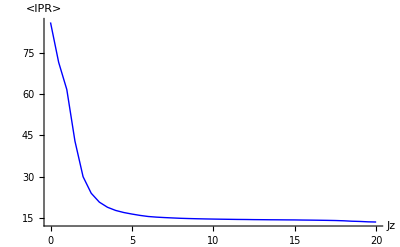

```mathematica
(*Parameters of the Hamiltonian*)
Clear[chainsize,upspins,downspins,dim,Jxy,Jz,open];
chainsize=10;
upspins=chainsize/2;
downspins=chainsize-upspins;
dim=chainsize!/(upspins!downspins!);
Jxy=1.0;
Jz=10;
open=1;
(*Creating the basis*)
Clear[onebasisvector,basis];
onebasisvector=Flatten[{Table[1,{k,1,upspins}],Table[0,{k,1,downspins}]}];
basis=Permutations[onebasisvector];

total = 41;
(*Loop for values of Jz*)
Do[
Jz=0.5 (kk-1);
(*ELEMENTS OF THE HAMILTONIAN*)
(*Initialization*)
Clear[HH];
Do[Do[HH[i,j]=0.,{j,1,dim}],{i,1,dim}];

(*Diagonal elements-Ising interaction*)
Do[
Do[
HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,k]]+basis[[i,k+1]]);
       ,{k,1,chainsize-1}];
,{i,1,dim}];
(*Term included in the Ising interaction if the chain is closed*)
If[open==0,
Do[HH[i,i]=HH[i,i]+(Jz/4.)*(-1.)^(basis[[i,chainsize]]+basis[[i,1]]),
{i,1,dim}]];

(*Off-diagonal elements-flip-flop term*)
Clear[howmany,site];
Do[
Do[
(*Initialization*)
howmany=0
Do[site[z]=0,{z,1,chainsize}];
(*Sites where states i and j differ*)
Do[If[basis[[i,k]]≠basis[[j,k]],{howmany=howmany+1,site[howmany]=k}];,{k,1,chainsize}];
(*Coupling matrix element-when only two neighbor sites differ*)
If[howmany==2,If[site[2]-site[1]==1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
(*Additional term for closed system*)If[open==0, If[site[2]-site[1]==chainsize-1,{HH[i,j]=HH[i,j]+Jxy/2.,HH[j,i]=HH[j,i]+Jxy/2.}]];
,{j,i+1,dim}];
,{i,1,dim-1}];

(* TOTAL HAMILTONIAN AND DIAGONALIZATION *)
Clear[Hamiltonian,Energy,Vector];
Hamiltonian=Table[Table[HH[i,j],{j,1,dim}],{i,dim}];
Energy=Eigenvalues[Hamiltonian];
Vector=Eigenvectors[Hamiltonian];

(*Inverse Participation Ratio:IPR*)

Clear[IPR];
IPR=0.0;
Do[
Clear[denom];
denom=Sum[Vector[[i,k]]^4,{k,1,dim}];
IPR=IPR+1/denom;
,{i,1,dim}];

(*Average value of IPR*)
AveIPR[kk]=IPR/dim;
Print[{Jz,AveIPR[kk]}];
,{kk,1,total}];

(*Plot:IPR vs Jz*)
Clear[tab];
tab=Table[{0.5 (kk-1),AveIPR[kk]},{kk,1,total}];
ListPlot[tab,Joined->True, LabelStyle->Directive[Black,Bold,Medium],PlotStyle->{Blue,Thick},AxesLabel->{"Jz","<IPR>"}, PlotRange->All]
```